F(1/11) = 12155/65536+(984555 (-1+x))/65536+(1640925 (-1+x)^2)/8192+(8423415 (-1+x)^3)/8192+(10830105 (-1+x)^4)/4096+(15643485 (-1+x)^5)/4096+(3318315 (-1+x)^6)/1024+(1640925 (-1+x)^7)/1024+109395/256 (-1+x)^8+12155/256 (-1+x)^9

F'(1/11) = 984555/65536+(1640925 (-1+x))/4096+(25270245 (-1+x)^2)/8192+(10830105 (-1+x)^3)/1024+(78217425 (-1+x)^4)/4096+9954945/512 (-1+x)^5+(11486475 (-1+x)^6)/1024+109395/32 (-1+x)^7+109395/256 (-1+x)^8

Roots of F are: {{x→0.},{x→-0.866025},{x→0.866025},{x→-0.34202-4.05759×10^-17 ⅈ},{x→0.34202+4.05759×10^-17 ⅈ},{x→-0.984808+0. ⅈ},{x→0.984808+0. ⅈ},{x→-0.642788-4.318×10^-17 ⅈ},{x→0.642788+4.318×10^-17 ⅈ}}

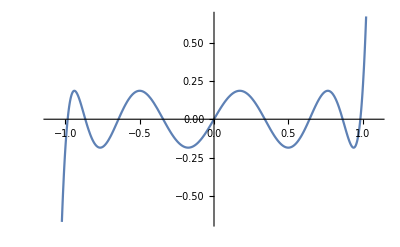

```mathematica
For [iOrder=9,iOrder≤9,iOrder++,
f[x_] := JacobiP[iOrder,-1/2,-1/2,x];
Print["F(1/11) = ",JacobiP[iOrder,-1/2,-1/2,x]];
Print["F'(1/11) = ",D[JacobiP[iOrder,-1/2,-1/2,x],x]];
Print["Roots of F are: ",N[Solve[JacobiP[iOrder,-1/2,-1/2,x]==0,x]]];
Plot[JacobiP[iOrder,-1/2,-1/2,x],{x,-1.1,1.1}]//Print;
Print[]
]
```